```mathematica
b :=0.2
k := 10^(-4)
f[x_]:=NIntegrate[i^2 * Exp[((x-1)*i^2-2*b*i^3/3)/k],{i,0,Infinity}]-(NIntegrate[i*Exp[((x-1)*i^2-2*b*i^3/3)/k],{i,0,Infinity}])^2
```

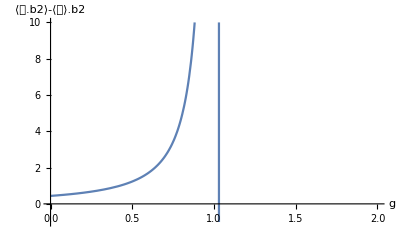

```mathematica
Plot[f[x]*10^6,{x,0,2},
AxesLabel->{"g","⟨𝑰.b2⟩-⟨𝑰⟩.b2"},
LabelStyle->{FontSize->14},
PlotRange->{{0,2},{-1,10}}]
```